```mathematica
(* THE VERY BASIC (1) *)
5/6
3+4
9^2
E^(I Pi)
Pi
N[Pi]
```

5/6

7

81

-1

π

3.14159

```mathematica
(* THE VERY BASIC (2) *)
```

```mathematica
3+4
%/2
N[%]
10*10==100
10<Exp[10]
10<Log[10]
```

7

7/2

3.5

True

True

False

```mathematica
(* THE VERY BASIC (3) *)
(x-1)(x+1)
Simplify[%] 

(x+1)(x+2)(x+3)
Expand[%]

x^10-1
Factor[%]
```

(-1+x) (1+x)

-1+x^2

(1+x) (2+x) (3+x)

6+11 x+6 x^2+x^3

-1+x^10

(-1+x) (1+x) (1-x+x^2-x^3+x^4) (1+x+x^2+x^3+x^4)

```mathematica
(* DEFINITION *)
```

1

2

3

2

Sin[x]

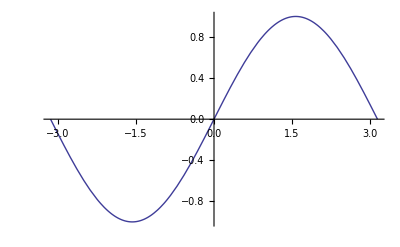

```mathematica
a=1
b=2
a+b
a*b
y=Sin[x]
Plot[y,{x,-Pi,Pi}]
```

-1

0

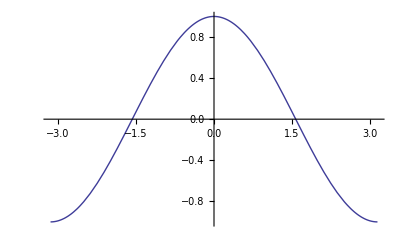

```mathematica
(* In the last case, you should instead "define a function". *)
f[x_]:=Cos[x]
f[Pi]
f[Pi/2]
Plot[f[x],{x,-Pi,Pi}]
```

```mathematica
(* Substitution (VERY IMPORTANT!) *)
y=Sin[x]+Cos[x]
```

Cos[x]+Sin[x]

```mathematica
y/.{x->4}
```

Cos[4]+Sin[4]

```mathematica
y/.Sin->Tan
```

Cos[x]+Tan[x]

```mathematica
y/.{Sin->Exp,x->4}
```

ⅇ^4+Cos[4]

```mathematica
ReplaceAll[y,x->4]
```

Cos[4]+Sin[4]

```mathematica
(* REPEATED substitution *)
```

```mathematica
energy=m*gamma
ReplaceAll[energy,{gamma->1/Sqrt[1-beta^2],beta->v/c}]
```

General::spell1: スペル間違いの可能性があります．新規シンボル"gamma"はすでにあるシンボル"Gamma"に似ています．

gamma m

General::spell1: スペル間違いの可能性があります．新規シンボル"beta"はすでにあるシンボル"Beta"に似ています．

m/(√(1-beta^2))

```mathematica
ReplaceRepeated[energy,{gamma->1/Sqrt[1-beta^2],beta->v/c}]
```

m/(√(1-v^2/c^2))

```mathematica
(* Or *)
energy//.{gamma->1/Sqrt[1-beta^2],beta->v/c}
```

m/(√(1-v^2/c^2))

```mathematica
(* EMERGENCY EXIT *)
(* ALT(or command)+period if you want to stop evaluation. *)
Integrate[(Sin[x]+Tan[x])^100,x]
(* You can stop evaluation from the menu: Evaluation>Abort Evaluation. *)
```

$Aborted

```mathematica
(* This is important when you induce an infinite-evaluation. *)
Sin[x]/.x->Sin[x]
Sin[x]//.x->Sin[x]
```

Sin[Sin[x]]

$Aborted

```mathematica
(* THAT'S MATHEMATICA BASIC. *)
(* Now Let's forget all == ABORT THE KERNEL. *)
```

```mathematica
energy
```

gamma m

```mathematica
Exit[]
(* Now the kernel has been initialized. *)
```

```mathematica
energy
(* is now undefined. *)
```

energy